## Equilibrium calculation

```mathematica
A[α_,γ_]:=(1-γ)/(α γ);
k[α_,γ_,r_]:=(r+1)/(A[α,γ] (r-1)+r)-1

equilibrium[r_,β_,α_,γ_,f_,type_]:=If[type==False,(*Type I uses this formula*)1/(k[α,γ,r]^(1/β)+1),(*Type II uses this formula*)(1/(k[α,γ,r]+1)-f)/(1-f)];
```

```mathematica
q2=3;q1=2;β=.;u=0;α=0.8;
```

```mathematica
{typ1 conf, anticonformist;} and {type 2 conformist, anticonformist} {type 2 mixed1.2}
```

2 type 2 mixed1.2 and anti anticonformist conf conformist^2 typ1 type

```mathematica
plt[i_]:=Plot[equilibrium[q2/q1,ToExpression[allparams⟦i,7,2⟧],α,γ,1/ToExpression[allparams⟦i,12,2⟧],types⟦i⟧],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.01]],Frame->True,AspectRatio->1,PlotLabel->ToString[folders⟦i⟧]];
```

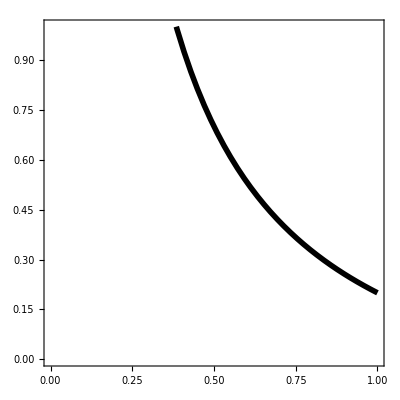

```mathematica
Plot[equilibrium[q2/q1,2,α,γ,1/2,True],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.01]],Frame->True,AspectRatio->1(*,PlotLabel->ToString[folders⟦i⟧]*)]
```

```mathematica
ListDensityPlot[allraw⟦8⟧⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},PlotLabel->ToString[folders⟦8⟧],ImagePadding->30]
```

Part::partd: Part specification allraw⟦8⟧ is longer than depth of object.

Part::partd: Part specification folders⟦8⟧ is longer than depth of object.

ListDensityPlot::arrayerr: 8. must be a valid array.

ListDensityPlot[8,PlotRange→All,PlotLegends→Placed[,Above],Frame→True,FrameStyle→Directive[GrayLevel[0],Thickness[0.003]],FrameLabel→{Probability of copying, γ,Initial frequency of low-quality morph},PlotLabel→folders[[8]],ImagePadding→30]

## Import data

```mathematica
SetDirectory[NotebookDirectory[]<>"../simulations/data/2morphs/"];
```

```mathematica
folders=FileNames[]
```

{typeI_anticonformist_b-0.1,typeI_anticonformist_b-1,typeI_anticonformist_b-2,typeI_conformist_r2,typeII_anticonformist_f1.2,typeII_anticonformist_f2,typeII_anticonformist_f2_longer,typeII_conformist_f1.2,typeII_conformist_f2,typeII_mixed_f1.2,typeII_mixed_f1.2_lowthreshold,typeII_mixed_f2_longer,typeII_mixed_f2_lowthreshold}

```mathematica
allraw={};
allparams={};
For[i=1,i≤Length[folders],i++,
raw=Import[folders⟦i⟧<>"/out.csv","CSV"];
params=Import[folders⟦i⟧<>"/params.csv","CSV"];
AppendTo[allraw,raw];
AppendTo[allparams,params];
]
```

```mathematica
allparams⟦8⟧
```

{{Parameter,Value},{n_population,100},{n_matings,100},{n_runs,50},{m,2},{T,25},{b,2},{y_range,[0.   0.01 0.02 0.03 0.04 0.05 0.06 0.07 0.08 0.09 0.1  0.11 0.12 0.13
 0.14 0.15 0.16 0.17 0.18 0.19 0.2  0.21 0.22 0.23 0.24 0.25 0.26 0.27
 0.28 0.29 0.3  0.31 0.32 0.33 0.34 0.35 0.36 0.37 0.38 0.39 0.4  0.41
 0.42 0.43 0.44 0.45 0.46 0.47 0.48 0.49 0.5  0.51 0.52 0.53 0.54 0.55
 0.56 0.57 0.58 0.59 0.6  0.61 0.62 0.63 0.64 0.65 0.66 0.67 0.68 0.69
 0.7  0.71 0.72 0.73 0.74 0.75 0.76 0.77 0.78 0.79 0.8  0.81 0.82 0.83
 0.84 0.85 0.86 0.87 0.88 0.89 0.9  0.91 0.92 0.93 0.94 0.95 0.96 0.97
 0.98 0.99 1.  ]},{q_values,[3 2]},{c_range,[0.   0.01 0.02 0.03 0.04 0.05 0.06 0.07 0.08 0.09 0.1  0.11 0.12 0.13
 0.14 0.15 0.16 0.17 0.18 0.19 0.2  0.21 0.22 0.23 0.24 0.25 0.26 0.27
 0.28 0.29 0.3  0.31 0.32 0.33 0.34 0.35 0.36 0.37 0.38 0.39 0.4  0.41
 0.42 0.43 0.44 0.45 0.46 0.47 0.48 0.49 0.5  0.51 0.52 0.53 0.54 0.55
 0.56 0.57 0.58 0.59 0.6  0.61 0.62 0.63 0.64 0.65 0.66 0.67 0.68 0.69
 0.7  0.71 0.72 0.73 0.74 0.75 0.76 0.77 0.78 0.79 0.8  0.81 0.82 0.83
 0.84 0.85 0.86 0.87 0.88 0.89 0.9  0.91 0.92 0.93 0.94 0.95 0.96 0.97
 0.98 0.99 1.  ]},{copying_type,2},{factor,2},{threshold_2m,0.7},{threshold_3m,0.5}}

```mathematica
types=StringMatchQ[ToString[#],"typeII"~~___]&/@folders
```

{False,False,False,False,True,True,True,True,True,True,True,True,True}

## Plotting and saving images

```mathematica
images={};
For[i=1,i≤Length[folders],i++,
dp=ListDensityPlot[allraw⟦i⟧⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},PlotLabel->ToString[folders⟦i⟧]];
image=Show[dp,plt[i]];
(*Export[folders⟦i⟧<>"/image.pdf",image];*)
AppendTo[images,image];
]
```

## Visualise it here

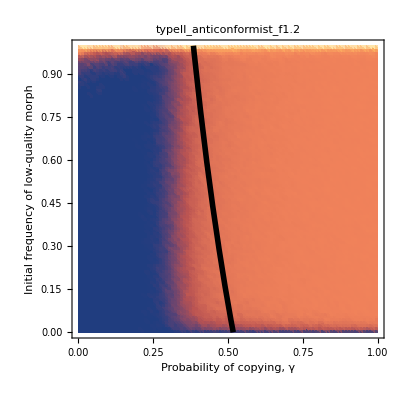

```mathematica
images⟦5⟧
```

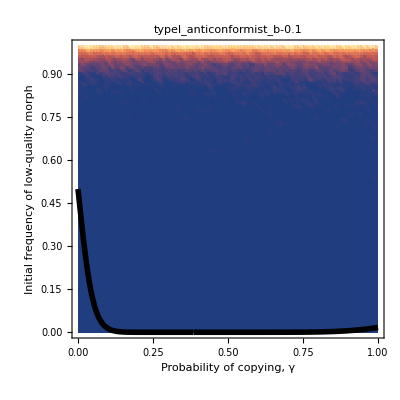
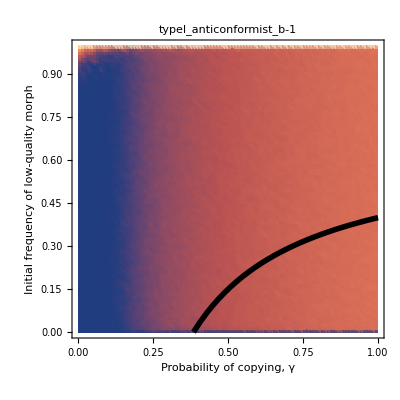
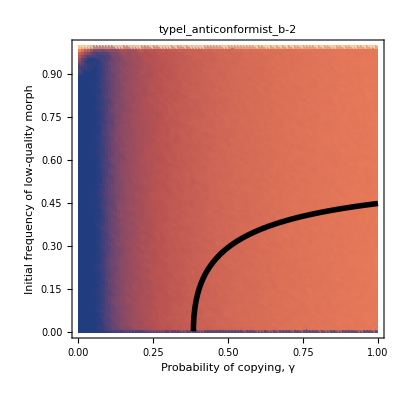
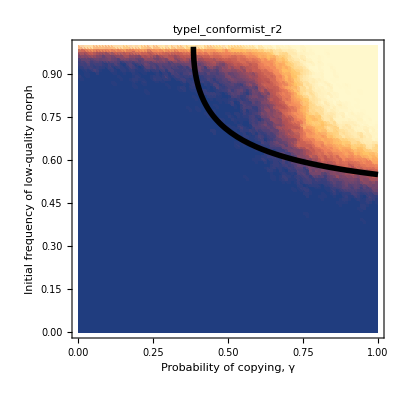
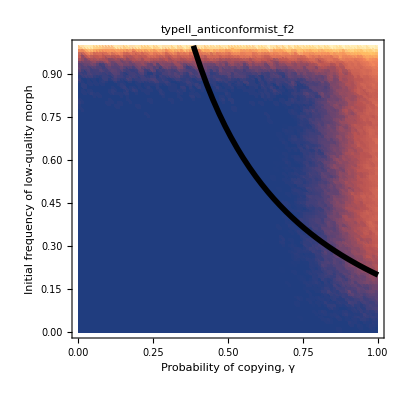
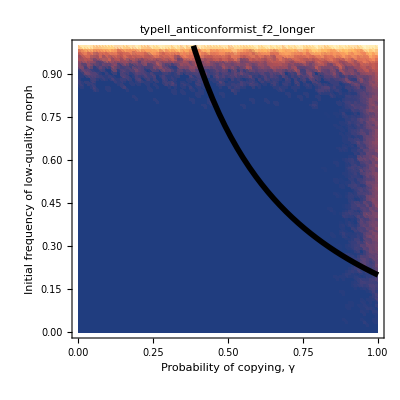
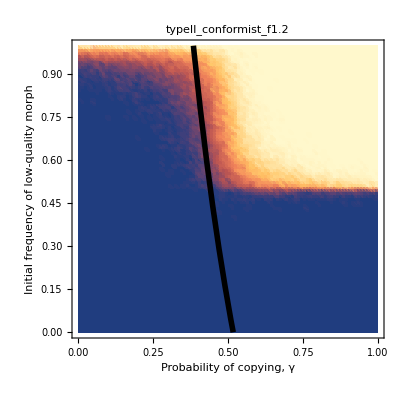
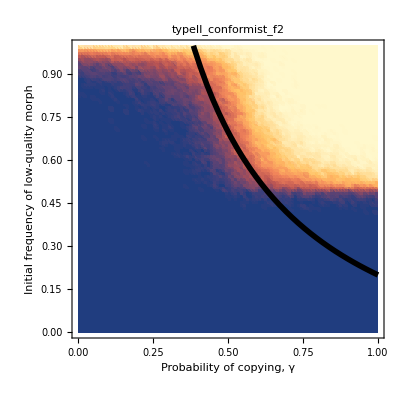
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[images⟦i⟧,{i,1,Length[images],1}]
```

```mathematica
GraphicsGrid[Partition[Table[images⟦i⟧,{i,1,Length[images],1}],3]]
```

-Graphics-